General::ChatbookInternal: An unexpected error occurred. …

Failure[…]

# BTC dollar cost averaging

```mathematica
Clear["Global`"];
SetDirectory[NotebookDirectory[]];
(*Buttons to hide/show code*)CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

```mathematica
settings=<|
aspectratio->1/3
,imagemargins->20
,imagesize->1000
,labelstyle->{18}
,origindate->"Sep. 14, 2011"
,plotbackground->Lighter[LightGray,0.75]
,subtitlestyle->{15}
,ticksstyle->{16}
,titlestyle->{20,Red}
|>;
st=StringTemplate;
dollar[a_]:=StringTemplate["$``"][NumberForm[a,DigitBlock->3]];
updatedstr=Style[StringTemplate["(updated: ``)"][DateString[]],settings[subtitlestyle]];
maniprange=Join[{1,2,3, 6, 9},Range[12,144,6]]//Reverse;
purchcost=0.03;
btcusd =FinancialData["BTC/USD",settings[origindate]];
nbtcusd=btcusd//Normal;
currentprice=Last[Last[nbtcusd]];
dca=<|date->#[[1]],price->#[[2]],infl->InflationAdjust[Quantity[1,DatedUnit["USDollars",#[[1]]]]],sats->IntegerPart[100000000*(1-purchcost)/#[[2]]]|>&/@nbtcusd;
cums=(MapIndexed[#1/#2&,Map[#1[sats]& , Reverse[dca]]//Flatten//N//Accumulate]//Flatten)*currentprice/100000000//Reverse;
dca[[All,"dcaperf"]]=cums;
pv[days_]:=(((#[sats]&/@(Take[dca,-days]))//Total)*currentprice/100000000)/days;
plotlabelstyles={20,16,14};
gridlinesx = Join[DateRange[{2010},{2030},Quantity[1,"Months"]],{#,Thick}&/@DateRange[{2010},{2030},Quantity[1,"Years"]]];
```

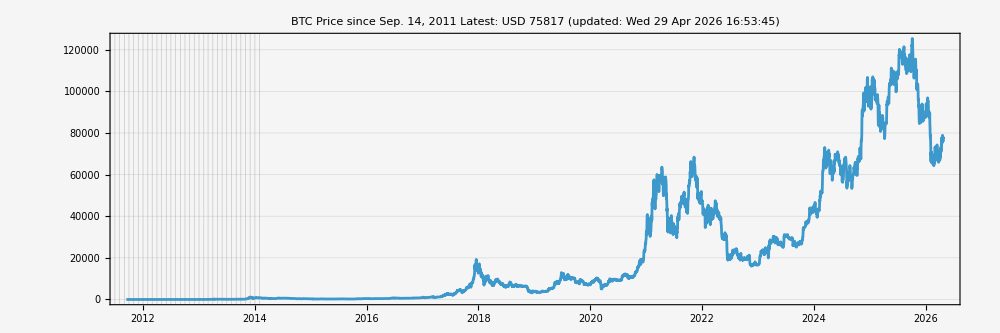

```mathematica
DateListPlot[
btcusd
,AspectRatio->settings[aspectratio]
,Background->settings[plotbackground]
,FrameTicks->All
,GridLines->{gridlinesx,Automatic}
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,LabelStyle->settings[labelstyle]
,PlotRange->Full
,TicksStyle->settings[ticksstyle]
,PlotLabel->Column[
{
Style[
"BTC Price since " <> settings[origindate ]
,settings[titlestyle]
]
,Style[
"Latest: USD " <> ToString[btcusd["LastValue"]//Round]
,settings[subtitlestyle]
]
,updatedstr
}
,Center
]
]
```

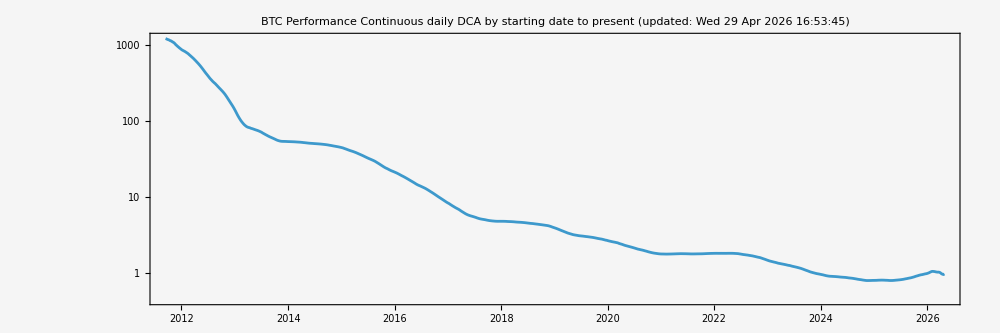

```mathematica
btcdcaperformance=DateListLogPlot[
{#[date],#["dcaperf"]}&/@dca
,AspectRatio->settings[aspectratio]
,Background->settings[plotbackground]
,FrameTicks->All
,GridLines->{gridlinesx,Join[Range[10],Range[20,100,10],Range[200,10000,100]]}
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,LabelStyle->settings[labelstyle]
,PlotRange->Full
, PlotLabel->Column[{
Style["BTC Performance", settings[titlestyle]]
, Style["Continuous daily DCA by starting date to present",settings[subtitlestyle]]
,updatedstr
}
,Center
]
];
filename = "BTC-DCA-Performance.jpg";
Export[filename,btcdcaperformance];
btcdcaperformance
```

```mathematica
maniprange=Join[
MapIndexed[#->ToString[First[#2]]<>" mo"&,{1,2,3, 6, 9}]
,MapIndexed[#->ToString[N[#1/12]]<>" yr"&,Range[12,144,6]]
]//Reverse;
ts={#[date],#["dcaperf"]}&/@ dca//TimeSeries;
Manipulate[
Module[{tsx},(
tsx=TimeSeriesWindow[ts,{Today-Quantity[x,"Months"],Today}];
DateListLogPlot[
tsx
,AspectRatio->settings[aspectratio]
,Background->settings[plotbackground]
,FrameTicks->All
,GridLines->{gridlinesx, Join[Range[0,10,0.1],Range[11,100,1]]}
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,LabelStyle->settings[labelstyle]
,PlotRange->Full
,PlotLabel->Column[
{
Style[
"Cumulative Daily DCA Performance"
,settings[titlestyle]
]
,updatedstr
},
Center
]
]
)]
, {
{x, 60, Style["Starting...back",16]}
, maniprange
}
]
```